```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory["~/Desktop/Work/analysis"]
```

SetDirectory::cdir: Cannot set current directory to /home/andrew/Desktop/Work/analysis.

$Failed

```mathematica
a[θ_,ϕ_]:=Sin[θ]Cos[ϕ];
b[θ_,ϕ_]:=Sin[θ]Sin[ϕ];
c[θ_,ϕ_]:=Cos[θ];
d[θ_,ϕ_]:=(2 a[θ,ϕ]^2-1)/(2 c[θ,ϕ]);
e[θ_,ϕ_]:=√(1-a[θ,ϕ]^2-d[θ,ϕ]^2)
```

```mathematica
sA[θ_,ϕ_]:={a[θ,ϕ],b[θ,ϕ],c[θ,ϕ]}
sB[θ_,ϕ_]:={d[θ,ϕ],e[θ,ϕ],-a[θ,ϕ]};
sC[θ_,ϕ_]:={-e[θ,ϕ],-c[θ,ϕ]-d[θ,ϕ],-b[θ,ϕ]};
sD[θ_,ϕ_]:={-a[θ,ϕ],-b[θ,ϕ],-c[θ,ϕ]};
sE[θ_,ϕ_]:={-d[θ,ϕ],-e[θ,ϕ],a[θ,ϕ]};
sF[θ_,ϕ_]:={e[θ,ϕ],c[θ,ϕ]+d[θ,ϕ],b[θ,ϕ]};
```

```mathematica
sA[1,1]//N
```

{0.454649,0.708073,0.540302}

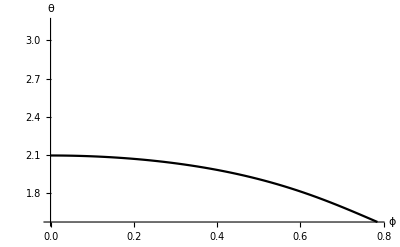

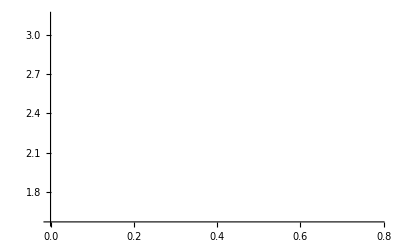

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[Sqrt[(4-Sqrt[16-6 (1-Cos[4 ϕ])])/(1-Cos[4 ϕ])]]]
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,0,π/4},PlotRange->{{0,π/4},{π/2,π}},PlotStyle->{Thick,Black},AxesLabel->{"ϕ","θ"}]
boundPlotWhite=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,0,π/4},PlotRange->{{0,π/4},{π/2,π}},Filling->Axis,FillingStyle->Opacity[1],PlotStyle->{White}]
```

```mathematica
views={{1,1,1},{1,-1,0},{-1,-1,0},{-1,-1,2}}
```

{{1,1,1},{1,-1,0},{-1,-1,0},{-1,-1,2}}

```mathematica
animate=Manipulate[Show[{Graphics3D[{Black,Arrowheads[0.1],Arrow[Tube[{{-1,-1,-1},{1,1,1}},0.01]]}],Graphics3D[{Red,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sA[θ,ϕ]},0.01]]}],Graphics3D[{Green,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sB[θ,ϕ]},0.01]]}],Graphics3D[{Blue,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sC[θ,ϕ]},0.01]]}],Graphics3D[{Pink,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sD[θ,ϕ]},0.01]]}],Graphics3D[{Brown,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sE[θ,ϕ]},0.01]]}],Graphics3D[{Purple,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sF[θ,ϕ]},0.01]]}]},AspectRatio->1,ViewPoint->{views[[v,1]],views[[v,2]],views[[v,3]]},ImageSize->{300,250}]
Show[boundPlot,ListPlot[{{ϕ,θ}}],ImageSize->{340,200}],{v,1,4,1},{θ,π/2+0.0000001,π,.01},{ϕ,0.0000001,π/4,0.01},ContentSize->{700,300}]
```

Part::partd: Part specification views⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification views⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification views⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["GroundStateView.avi",animate,"Framerate"->60]*)
```

```mathematica
vol[t_,p_]:=Dot[sA[t,p],Cross[sB[t,p],sC[t,p]]]
```

```mathematica
θmin=π/2;
θmax=π;
ϕmin=0;
ϕmax=π/4;
θsize=90;
ϕsize=90;
vsetsize=θsize*ϕsize;
voldata=Table[,{i,1,vsetsize}];
θ=θmin;
ϕ=ϕmin;
i=1;
θs=(θmax-θmin)/θsize;
ϕs=(ϕmax-ϕmin)/ϕsize;
Do[Do[If[θ>π-Bound[ϕ],voldata[[i]]={ϕ,θ,Abs[vol[θ,ϕ]]};i=i+1],{θ,θmin,θmax,θs}],{ϕ,ϕmin,ϕmax,ϕs}];
voldata=Select[voldata,UnsameQ[#,Null]&];
```

```mathematica
forbidden=RegionPlot[θ<π-Bound[ϕ]&&θ>π/2&&ϕ<π/4,{ϕ,0,π/4},{θ,π/2,π},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"ϕ","θ"}];
```

```mathematica
planarborder=ParametricPlot[{π/4 Cos[γ]+0.001,π/4 Sin[γ]+π/2+0.01},{γ,0,π/2},PlotStyle->{RGBColor[0.5,0.93,0.5]}];
```

```mathematica
π/4 Sin[π/2]+π/2//N
```

2.35619

```mathematica
π-Bound[0]+π/12//N
```

2.35619

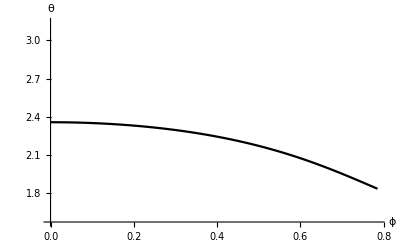

```mathematica
boundborder=Plot[{Bound[ϕ],π-Bound[ϕ]+π/12},{ϕ,0,π/4},PlotRange->{{0,π/4},{π/2,π}},PlotStyle->{Thick,Black},AxesLabel->{"ϕ","θ"}]
```

```mathematica
Show[{ListContourPlot[voldata,InterpolationOrder->1,PlotLegends->Automatic,Contours->30,AxesLabel->{"ϕ","θ"}],boundPlotWhite,boundPlot,planarborder},FrameLabel->{"ϕ","θ"}]
```

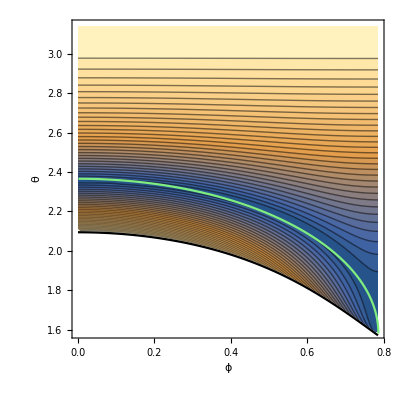

```mathematica
animate2=Manipulate[Show[{Graphics3D[{Black,Arrowheads[0.1],Arrow[Tube[{{-1,-1,-1},{1,1,1}},0.01]]}],Graphics3D[{Red,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sA[θ,ϕ]},0.01]]}],Graphics3D[{Green,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sB[θ,ϕ]},0.01]]}],Graphics3D[{Blue,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sC[θ,ϕ]},0.01]]}],Graphics3D[{Pink,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sD[θ,ϕ]},0.01]]}],Graphics3D[{Brown,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sE[θ,ϕ]},0.01]]}],Graphics3D[{Purple,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sF[θ,ϕ]},0.01]]}]},AspectRatio->1,ViewPoint->{views[[v,1]],views[[v,2]],views[[v,3]]},ImageSize->{300,300}]
Show[ListContourPlot[voldata,InterpolationOrder->1,PlotLegends->Automatic],boundPlotWhite,boundPlot,ListPlot[{{ϕ,θ}}],ImageSize->{340,200}],{v,1,4,1},{θ,π/2+0.0000001,π,.01},{ϕ,0.0000001,π/4,0.01},ContentSize->{800,300}]
```